## Bayesian Statistics, Exam 3

## Friday, Dec. 13, 2024 — Bayesian Conjugates and Monte Carlo Methods

## 1. A Beta Distribution Prior for Basketball Players Shooting 3-Pointers

An increasingly important shot in basketball is the “3-pointer.” In the NBA, this is a shot made from more than 23 feet 9 inches from the basket. There is a stripe on the court marking this distance. An average offensive player that shoots 3-pointers succeeds 30% of the time. (Otherwise you might as well just go for 2-pointers, which offensive players can make about 45% of the time.)

The beta distribution is:

((x^(α-1)(1-x))^(β-1))/(B(α,β))

The mean of the beta distribution with parameters α and β is μ=α/(α+β).

 The variance of the distribution is kind of a mess. It is σ^2=αβ/((α+β)^2(α+β+1)).

A. Let’s assume we have followed a bunch of players and their mean success rate μ=0.3. What combination of integers α and β will give μ=0.3? HINT: If you can’t just guess the combination of integers that works, try α=3 and see what β has to be.



B. What is the variance with the α and β you chose in Part A? Feel free to leave your answer for σ^2 as a rational fraction.


C. It turns out that the fraction you just calculated in B comes out to about σ^2=0.02 and taking the square root of that, you get a standard deviation, σ=0.14. On the plot below, draw three nice vertical lines at μ, at μ+σ, and at μ-σ. Shade in the region under the curve between these lines.

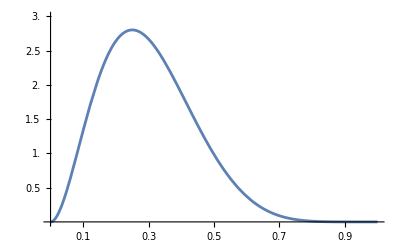

```mathematica
beta[x_]:=(x^(3-1)(1-x)^(7-1))/Beta[3, 7]
Plot[beta[x],{x,0,1}, PlotRange->{{0.0,1.0},{0.0,3.0}},Ticks->{Range[0.1,1.0,0.1],Range[0.5,3.0,0.5]}]
```

D. Make an estimate of the width, the average height, and the area you have shaded in.


E. Convert your answer to D into an estimate of the percentage of players that make 3-pointers between 16% and 34% of the time.


F. To finish off your analysis of the prior, write it out with the α and β you have chosen:

prior(x)=((x^(α-1)(1-x))^(β-1))/(B(α,β))=

## 2. A Likelihood for Nikola Jokic

On Dec. 8, Nikola Jokic of the Denver Nuggets made 3 out of 6 of the 3-pointers that he attempted against the Atlanta Hawks.

The formula for the binomial distribution is

L(x)=(N
n)(x^n(1-x))^(N-n)

You don’t know x. It is whatever Nikola Jokic’s true average is, and you don’t know that, so just leave x as a variable. But simplify L(x) as much as you can:

L(x)=

Now you have a likelihood.

## 3. A Posterior for Nikola Jokic

A. Take the product of the prior from Problem 1 and the likelihood from Problem 2. Simplify it as much as you can, but note that the denominator is a mess, so just leave it as denominator.

posterior(x)=(prior(x)*L(x))/denominator


B. Leave all the constants out and the messy denominator out. All that is left is powers of x and 1-x. What is left?

posterior(x)∝

C. This is another beta distribution. What are the α and β of this distribution?


D. Using your new α and β, you now have a probability distribution for Nikola Jokic’s average. What is 

μ=α/(α+β)=

for this new distribution? You can leave it as a rational fraction.

E. What is the variance

σ^2=αβ/((α+β)^2(α+β+1))=


for this new distribution? You can leave the variance as a rational fraction too.

Name ______________________________________

1.              / 3
2.              / 3
3.              / 4
4.              / 5

TOTAL          / 15